```mathematica
SeedRandom[6];
w=RandomVariate[CircularUnitaryMatrixDistribution[6]];
meshes=AssociationMap[QuantumInterferometer[w,Method->#]&,{"Clements","Reck","CosineSine"}]
```

<|Clements→QuantumInterferometer[…],Reck→QuantumInterferometer[…],CosineSine→QuantumInterferometer[…]|>

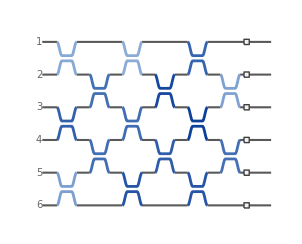
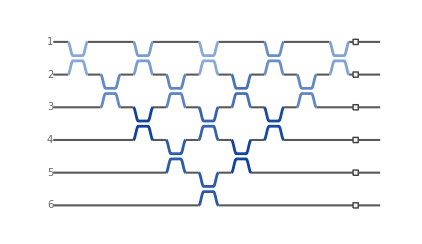
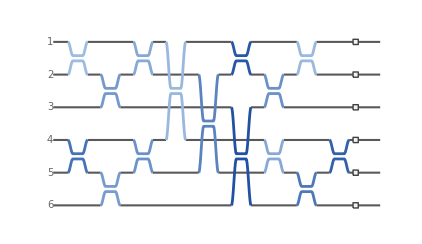

```mathematica
Column[KeyValueMap[Labeled[#2["Diagram"],#1,Top]&,meshes]]
```

```mathematica
Chop[{#["BeamSplitterCount"],#["PhaseShifterCount"],#["Depth"],Max[Abs[QuantumInterferometer[#["Elements"],6]["Unitary"]-w]]}]&/@meshes
```

<|Clements→{15,6,6,0},Reck→{15,6,9,0},CosineSine→{15,6,9,0}|>

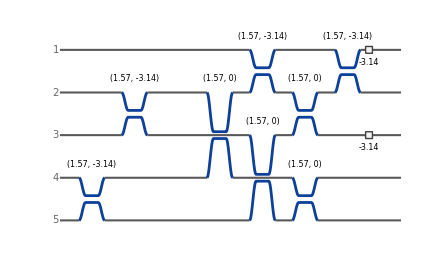

```mathematica
QuantumInterferometer[PermutationMatrix[{4,5,1,2,3}],Method->"CosineSine"]["Diagram","ShowParameters"->True]
```

```mathematica
mz=QuantumInterferometer[{"BS"[Pi/4,0]->{1,2},"PS"[φ]->1,"BS"[Pi/4,0]->{1,2}},2]
mz[{1,0}]
```

QuantumInterferometer[…]

<|1,0→-1/2+ⅇ^(ⅈ φ)/2,0,1→1/2+ⅇ^(ⅈ φ)/2|>

```mathematica
mz[{1,0}]
```

<|1,0→-1/2+ⅇ^(ⅈ φ)/2,0,1→1/2+ⅇ^(ⅈ φ)/2|>

```mathematica
hom["Diagram"]
```

-Graphics-

```mathematica
qi=QuantumInterferometer[{"BS"[Pi/4,0]->{1,2}},2];
in=(FockState[{1,0},2]+FockState[{0,1},2])["Normalized"]
out=qi[in]//TraditionalForm
```

QuantumState[…]

01

```mathematica
{hom[{1,1}],hom["Probabilities",{1,1}]}
```

{<|20→-1/(√2),02→1/(√2)|>,<|20→1/2,11→0,02→1/2|>}

```mathematica
QuantumInterferometer[{"BS"[θ,φ]->{1,2}},2][{1,1}]
```

<|2,0→-√2 ⅇ^(-ⅈ φ) Cos[θ] Sin[θ],1,1→Cos[θ]^2-Sin[θ]^2,0,2→√2 ⅇ^(ⅈ φ) Cos[θ] Sin[θ]|>

```mathematica
coincidence=FullSimplify[QuantumInterferometer[{"BS"[θ,φ]->{1,2}},2]["Probability",{1,1}->{1,1}],(θ|φ)∈Reals]
```

Cos[2 θ]^2

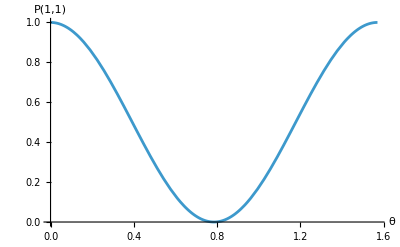

```mathematica
Plot[coincidence,{θ,0,Pi/2},AxesLabel->{"θ","P(1,1)"}]
```

```mathematica
tritter=QuantumInterferometer[FourierMatrix[3]];
tritter["Elements"]
```

{BS[π/4,(2 π)/3]→{1,2},BS[ArcTan[√2],(2 π)/3]→{2,3},BS[π/4,-(5 π)/6]→{1,2},PS[-π/6]→{1},PS[-π]→{2},PS[(2 π)/3]→{3}}

```mathematica
tritter["Probabilities",{1,1,5}]//RepeatedTiming
```

{0.0530741,<|700→14/729,610→32/729,601→32/729,520→8/243,511→1/27,502→8/243,430→10/729,421→0,412→0,403→10/729,340→10/729,331→10/729,322→20/243,313→10/729,304→10/729,250→8/243,241→0,232→20/243,223→20/243,214→0,205→8/243,160→32/729,151→1/27,142→0,133→10/729,124→0,115→1/27,106→32/729,070→14/729,061→32/729,052→8/243,043→10/729,034→10/729,025→8/243,016→32/729,007→14/729|>}

```mathematica
tritter["CircuitOperator",8]
```

QuantumCircuitOperator[<|Elements -> {QuantumOperator[QuantumState[SparseArray[<308>, {4096}], QuantumBasis[<|Input -> QuditBasis[<|{QuditName[0, Dual -> True], 1} -> SparseArray[<1>, {8}], {QuditName[1, Dual -> True], 1} -> SparseArray[<1>, {8}], {QuditName[«2»], 1} -> «1», «12», {QuditName[7, Dual -> True], 2} -> SparseArray[<1>, {8}]|>], «4»|>]], {«2»}], «5»}, Label -> «1»|>]

```mathematica
%[FockState[{1,1,5},8]]["Probability"]//RepeatedTiming
```

{0.0625346,<|007→14/729,016→32/729,025→8/243,034→10/729,043→10/729,052→8/243,061→32/729,070→14/729,106→32/729,115→1/27,133→10/729,151→1/27,160→32/729,205→8/243,223→20/243,232→20/243,250→8/243,304→10/729,313→10/729,322→20/243,331→10/729,340→10/729,403→10/729,430→10/729,502→8/243,511→1/27,520→8/243,601→32/729,610→32/729,700→14/729|>}

```mathematica
SeedRandom[7];
qi=QuantumInterferometer["Random"[3]];
out=qi[FockState[{1,1,0},3]];
Max@Abs@Normal[out["StateVector"]-qi["CircuitOperator",3][FockState[{1,1,0},3]]["StateVector"]]
```

2.77556×10^-16

```mathematica
SeedRandom[8];
sampler=QuantumInterferometer["Random"[8]];
probs=sampler["Probabilities",{1,1,1,1,0,0,0,0}];
{Length[probs],Total[probs],TakeLargest[probs,3]}
```

{330,1.,<|10001020→0.0313629,11010010→0.0283992,13000000→0.0257898|>}

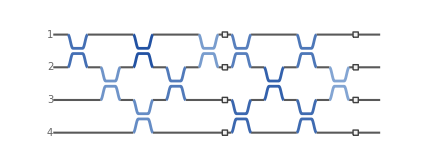

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
SeedRandom[9];
qi1=QuantumInterferometer["Random"[4],Method->"Reck"];
qi2=QuantumInterferometer["Random"[4]];
qi2[qi1]["Diagram"]
qi2[qi1]["Unitary"]-qi2["Unitary"].qi1["Unitary"]
```

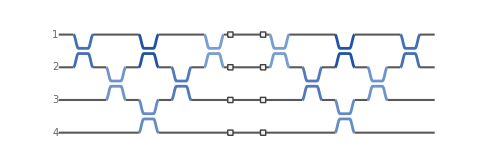

```mathematica
qi1["Dagger"][qi1]["Diagram"]
```

```mathematica
Chop[qi1["Dagger"][qi1]["Unitary"]]==IdentityMatrix[4]
```

True

```mathematica
qI = QuantumInterferometer[{"PS"[0.3]->1,"PS"[1.2]->1,"BS"[Pi/4,Pi/2]->{1,2},"BS"[0.4]->{1,3},"PS"[2.]->3},3]
```

QuantumInterferometer[…]

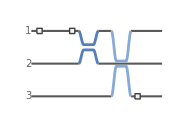

```mathematica
qI["Diagram"]
```

```mathematica
qI["ElementTable"]
```

### Relation to GBS

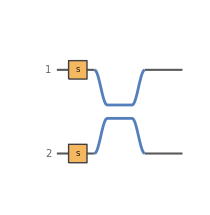

```mathematica
tmsv=QuantumInterferometer[{"S"[0.5]->1,"S"[-0.5]->2,"BS"[Pi/4,0]->{1,2}},2];
tmsv["Diagram"]
```

```mathematica
tmsv["Probabilities",{0,0}]
```

<|00→0.786448,20→4.66254×10^-35,11→0.167948,02→4.66254×10^-35,40→4.14635×10^-69,31→2.98709×10^-35,22→0.0358656,13→2.98709×10^-35,04→4.14635×10^-69,60→4.09701×10^-103,51→4.42731×10^-69,42→1.2758×10^-35,33→0.00765918,24→1.2758×10^-35,15→4.42731×10^-69,06→4.09701×10^-103,80→4.25067×10^-137,71→6.12448×10^-103,62→2.83639×10^-69,53→4.54083×10^-36,44→0.00163564,35→4.54083×10^-36,26→2.83639×10^-69,17→6.12448×10^-103,08→4.25067×10^-137,100→4.5361×10^-171,91→1.66958×10^-39,82→1.2021×10^-37,73→4.61606×10^-35,64→0.,55→0.000349294,46→1.43611×10^-34,37→5.12895×10^-36,28→1.92336×10^-36,19→4.17395×10^-40,010→4.5361×10^-171|>

```mathematica
tmsv["Probabilities",{0,0},"Cutoff"->6]
```

<|00→0.786448,20→4.66254×10^-35,11→0.167948,02→4.66254×10^-35,40→4.14635×10^-69,31→2.98709×10^-35,22→0.0358656,13→2.98709×10^-35,04→4.14635×10^-69,60→4.09701×10^-103,51→4.42731×10^-69,42→1.2758×10^-35,33→0.00765918,24→1.2758×10^-35,15→4.42731×10^-69,06→4.09701×10^-103|>

```mathematica
Select[tmsv["Probabilities",{0,0},"Cutoff"->6],#>10^-12&]
```

<|00→0.786448,11→0.167948,22→0.0358656,33→0.00765918|>

Closed form:

```mathematica
Table[Tanh[0.5]^(2 n)/Cosh[0.5]^2,{n,0,3}]
```

{0.786448,0.167948,0.0358656,0.00765918}

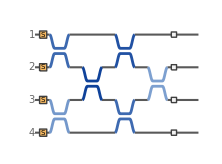

```mathematica
SeedRandom[1];
squeezers=QuantumInterferometer[Thread["S"[0.6]->Range[4]]];
gbs=QuantumInterferometer["Random"[4]][squeezers];   
gbs["Diagram"]
```

```mathematica
probs=gbs["Probabilities",{0,0,0,0},"Cutoff"->4];
TakeLargest[probs,5]
```

<|0000→0.506343,1001→0.052111,0101→0.0504282,0011→0.0408252,0020→0.033153|>

Hafnian result:

```mathematica
gbs["Amplitude",{0,0,0,0}->{1,1,1,1}]
```

0.0355256-0.0905235 ⅈ

Circuit:

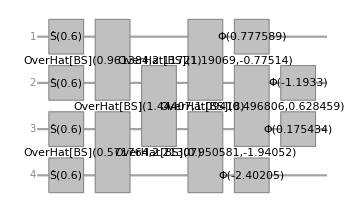

```mathematica
d=6;
gbs["CircuitOperator",d]
```

```mathematica
gbs["CircuitOperator",d][]
```

QuantumState[…]

```mathematica
(SuperDagger[FockState[{1,1,1,1},d]]@ %)["Scalar"]
```

0.0355256-0.0905235 ⅈ